```mathematica
N'[t]== N[t]*((r*S/(K + S))-D)

S'[t]== D(S0-S)-(N*r*S)/((K+S)*Y)
```

{{d→InterpolatingFunction[{{0.,24.}},<>],c→InterpolatingFunction[{{0.,24.}},<>]}}

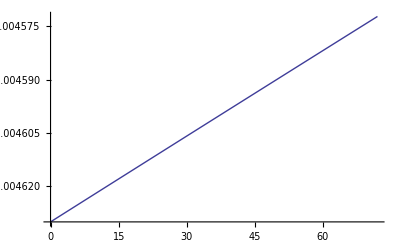

```mathematica
r=growth rate
S=resource concentration
K=half saturation constant of species N
S0=initial concentration of resource S
Y=yield of species N (cells/unit)
D=ln(1/(1-f))
f=flow growth rate



sol1=NDSolve[{d'[t]==d[t]*(((0.0000926*c[t])/(1000+c[t]))-.000089), c'[t]== .000089*(200-c[t])-(d[t]*0.0000926*c[t])/(200+c[t]), d[0]==100,c[0]==200},{d,c},{t,0,24}]

Plot[Evaluate[{c'[t]}/.sol1],{t,0,72}]
```